```mathematica
Integrate[r^2 ⅇ^(-r/(x Sin[θ])),{r,rmin,rmax}]
```

-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ]))

```mathematica
Integrate[r^2/Sin[θ]^2 ⅇ^(-r/Sin[θ]),{r,0,∞},{θ,0,π}]
```

4

```mathematica
Integrate[r^2/Sin[θ]^2 ⅇ^(-r/(7Sin[θ])),{r,0,∞},{θ,0,π}]
```

1372

```mathematica
Integrate[r^2/Sin[θ]^2 ⅇ^(-r/(x Sin[θ])),{r,0,∞},{θ,0,π}]
```

ConditionalExpression[4 x^3,Re[x]>0&&Im[x]==0]

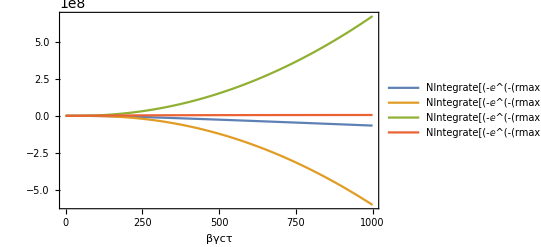

```mathematica
Block[{rmin=10^-4 500,rmax=162,θmin=17 Degree,θmax=150 Degree},Plot[{NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2))/Sin[θ]^2,{θ,θmin,θmax}],NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 x Sin[θ] rmax)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] ( (2 x Sin[θ] rmin)))/Sin[θ]^2,{θ,θmin,θmax}],NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2)+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (2 (x Sin[θ])^2 ))/Sin[θ]^2,{θ,θmin,θmax}],NIntegrate[(-ⅇ^(-(rmax Csc[θ])/x) x Sin[θ] (rmax^2+2 x Sin[θ] (rmax+x Sin[θ]))+ⅇ^(-(rmin Csc[θ])/x) x Sin[θ] (rmin^2+2 x Sin[θ] (rmin+x Sin[θ])))/Sin[θ]^2,{θ,θmin,θmax}]},{x,0,1000},Frame->True,PlotLegends->"Expressions",PlotRange->Full,FrameLabel->{"βγcτ",""}]]
```